# Collective Attention

Three papers on collective attention by Huberman et al.

## Attention Threshold

Attention Threshold in twitter Trending Topics
Chunyan Wang, Bernado A. Huberman.(2011) Long Trend Dynamics in Social Media

```mathematica
(*Discrete time Model*
Denote the cumulative number of first time posts (FTP)mentioning a given topic at a given time t by Subscript[N, t];
  Subscript[x, t] is assumed to be samll, positive, independent and identically sistributed random variables with mean μ and variance σ^2
*)
```

```mathematica
SolveAlways[ⅇ^x==1+x, x]
```

{}

```mathematica
SolveAlways[x==Log[1+x], x]
```

SolveAlways::ifun: Inverse functions are being used by SolveAlways, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Reduce[ⅇ^x==1+x, x]
```

(C[1]∈Integers&&x==-1-ProductLog[C[1],-1/ⅇ])||x==0

```mathematica
(∑_(k=0)^∞ (1-p)^k*p*k)//FullSimplify
```

-1+1/p

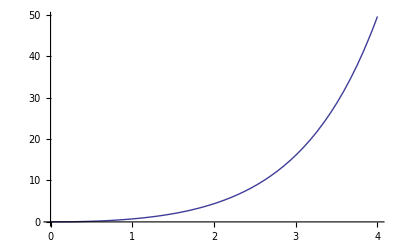

```mathematica
Plot[ⅇ^x-1-x, {x, 0, 4}]
```

```mathematica
Series[Exp[x],{x,0,4}]  (*Talor series*)
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
Plot[PDF[UniformDistribution[{-4,4}],x],{x,-4,4}];
```

## Feedback Loops of attention

```mathematica
P(stop after n)=(N(n))/(∫_n^Subscript[n, max] N(m)ⅆm)=n^-k/(∫_n^Subscript[n, max] m^-k ⅆm)
```

```mathematica
(n^-k/(∫_n^Subscript[n, max] m^-k ⅆm))//FullSimplify
```

n^-k/If[((Im[n]≥Im[n_max]&&Im[n_max] Re[n]≤Im[n] Re[n_max])||(Im[n_max] Re[n]≥Im[n] Re[n_max]&&Im[n]≤Im[n_max]))&&(n/(n-n_max)∉Reals||(Re[n/(-n+n_max)]≥0&&n/(n-n_max)≠0)||Re[n/(n-n_max)]≥1),(n^(1-k)-n_max^(1-k))/(-1+k),Integrate[m^-k,{m,n,n_max},Assumptions→!(((Im[n]≥Im[n_max]&&Im[n_max] Re[n]≤Im[n] Re[n_max])||(Im[n_max] Re[n]≥Im[n] Re[n_max]&&Im[n]≤Im[n_max]))&&(n/(-n+n_max)∉Reals||(Re[n/(-n+n_max)]≥0&&n/(n-n_max)≠0)||Re[n/(n-n_max)]≥1))]]

```mathematica
Im[2+3I]  (* Im give the imaginary part of complex number*)
```

```mathematica
n^-k/(∫_n^Subscript[n, max] m^-k ⅆm)=1/n+(n/Subscript[n, max])^(-k+1)   (*I have questions about how to derive this equation*)
```

## Novelty and Collective Attention

```mathematica
(* Popularity growth, the more popular the news becomes, the faster it spreads, this is the positive-reinforcement effect)
(* Novelty decay, the novelty of the story fade with time)
(* However, it's not only the attention, actually, it's more than attention, digg means perception, taste, and sharing)
```

### LogNormal

```mathematica
PDF[LogNormalDistribution[μ,σ],x];
```

```mathematica
Plot[PDF[LogNormalDistribution[0,1],x],{x,0,5}];
```

```mathematica
Plot[PDF[LevyDistribution[0,1],x],{x,0,5}]; (* LevyDistribution could generate iid variables.
```

```mathematica
(* Subscript[N, t] the number of diggs at time t is log-normal distribution, which could be explained by a stochastic dynamical model.
```

```mathematica
(* Subscript[X, t] is iid random variables with mean μ,and standard diviation σ, and Subscript[X, t]>0.
```

```mathematica
(* μ the percentage of people who spread the news to their friends.
```

```mathematica
Subscript[N, t]=(1+Subscript[X, t])Subscript[N, t-1]
```

```mathematica
(* Subscript[r, t] is time dependent, Subscript[r, t]>0, Subscript[r, 1]=1, and when Subscript[r, t]->0, t->∞.
```

```mathematica
Subscript[N, t]=(1+Subscript[r, t] Subscript[X, t])Subscript[N, t-1]  (* news propagation->news diffusion.
```

```mathematica
Subscript[N, t]=∏_(s=1)^t (1+Subscript[r, s] Subscript[X, s])Subscript[N, 0] OverTilde[=] ∏_(s=1)^t e^(Subscript[r, s] Subscript[X, s])Subscript[N, 0]= e^(∑_(s=1)^t Subscript[r, s] Subscript[X, s])Subscript[N, 0]                                            (*[1]
```

```mathematica
(* Series[Exp[x],{x,0,4}]  (*Talor series*)
```

```mathematica
Log[Subscript[N, t]]-Log[Subscript[N, 0]]=∑_(s=1)^t Subscript[r, s] Subscript[X, s]                                                                                      (*[2]
```

### Distribution

```mathematica
ExpectedValue[Log[Subscript[N, t]]-Log[Subscript[N, 0]]]=(∑_(s=1)^t (Log[Subscript[N, s]]-Log[Subscript[N, 0]]))/t =(∑_(s=1)^t (∑_(s=1)^t Subscript[r, s] Subscript[X, s]  ))/t
```

```mathematica
Refine[(∑_(s=1)^t (∑_(s=1)^t Subscript[r, s] Subscript[X, s]  ))/t ,Assumptions->(∑_(s=1)^t Subscript[X, s])/t==μ]
```

(∑_(s=1)^t (∑_(s=1)^t r_s X_s))/t

```mathematica
FullSimplify[(∑_(s=1)^t (∑_(s=1)^t Subscript[r, s] Subscript[X, s]  ))/t ,Element[t|s,Integers]&&Subscript[r, s]>0&&Subscript[r, 1]==1&&Limit[Subscript[r, s],s->Infinity]==0&&(∑_(s=1)^t Subscript[X, s])/t==μ]
```

General::ivar: 1 is not a valid variable.

(∑_(s=1)^t (∑_(s=1)^t r_s X_s))/t

```mathematica
Limit[(1+x/n)^n,n->Infinity]
```

ⅇ^x